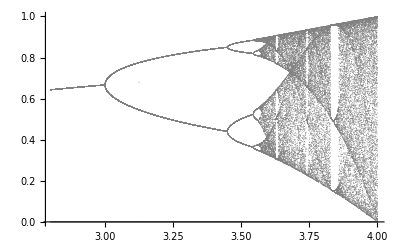

```mathematica
ListPlot[Table[Thread[{r,Nest[r # (1-#)&,Range[0,1,0.01],2000]}],{r,2.8,4,0.001}],PlotStyle->Directive[Gray,PointSize[0.00001]]]
```